This file is not published.
Run the file Solver N=2* SYM numeric first.

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`

defaultplotstyle=("DefaultPlotStyle"/. (Method/.Charting`ResolvePlotTheme[Automatic,Plot]));
```

## Root test

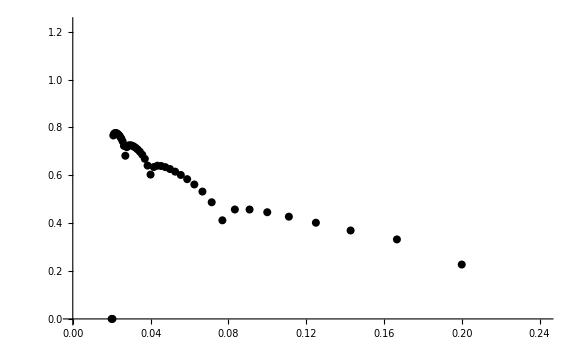

```mathematica
Table[{1/ll,π^2 Abs[Wλ[1,ll]]^(1/ll)},{ll,cutoffλ}];
ListPlot[%,AxesLabel->{MaTeX["1/\\ell"],MaTeX["\\frac{\\mathbb{W}_{\\ell+1}(2\\pi)}{16\, \\mathbb{W}_{\\ell}(2\\pi)}"],Black},PlotStyle->{Black,PointSize[0.01]},ImageSize->Large]
```

## Save/load

```mathematica
(* Save[NotebookDirectory[]<>"Solver N=2star SYM numeric (cont).mx","Global`"]; *)
```

```mathematica
(* <<(NotebookDirectory[]<>"Solver N=2star SYM numeric (cont).mx"); *)
```